```mathematica
euler=ReadList["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab6\\lab6\\ImplicitEuler.txt",Number,RecordLists->True];
```

```mathematica
k=10;m=1;T=10;
```

```mathematica
sol=DSolve[{x'[t]==y[t],y'[t]==-k/m x[t],x[0]==2,y[0]==0},{x[t],y[t]},t];
```

```mathematica
fun = Table[sol[[1]][[i]][[2]],{i,1,Length[sol[[1]]]}];
```

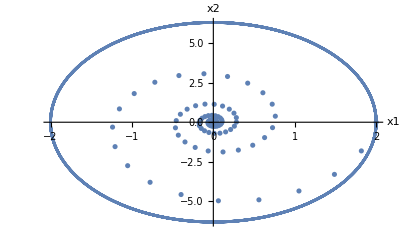

```mathematica
Show[ListPlot[euler, PlotRange->All, AxesLabel->{"x1","x2"}],ParametricPlot[fun,{t,0,T}] , PlotRange->All]
```